First Lowest eigenstates for the Quantum Harmonic Oscillator by Exact Diagonalization of the Hamiltonian
Óscar Amaro (Mar 2024)

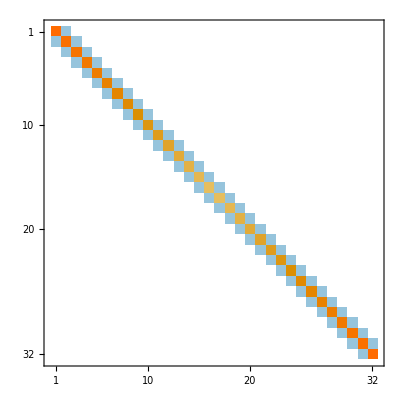

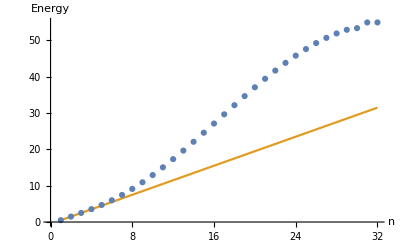

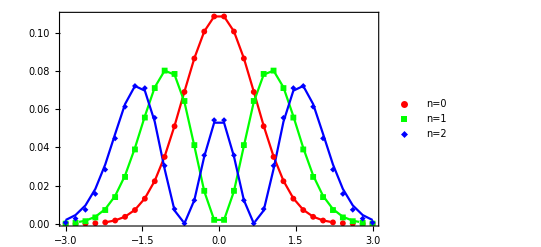

```mathematica
Clear[n,Nv,α,FN,FNinv,H,x,σ,GS,E0,E1,E2,psi,xt,Hd,th0,th1,th2,dx,Id,V,K]

n=5;(*number of qubits*)
Nv=2^n;(* grid size*)
α=1/((0.5-Nv/2)^2);(*normalization of x-domain*)
x=3Table[Sqrt[α](i+0.5-Nv/2),{i,0,Nv-1,1}];(*x-domain*)
dx = x[[2]]-x[[1]];
Id=IdentityMatrix[Nv];

(* kinetic energy *)
K=Id*0;
For[i=1,i<=Nv,i++,
If[i>1,K[[i,i-1]]=1];
K[[i,i]]=-2;
If[i<Nv,K[[i,i+1]]=1;];
];
K=-0.5K/dx^2;

V=0.5DiagonalMatrix[x^2];(* quadratic potential energy *)

H=V+K;(* hamiltonian *)
H//MatrixPlot (* plot matrix *)

{eval,evec}=Transpose[Sort[Transpose[Eigensystem[H]]]];(*get sorted eigensystem *)
ListPlot[{eval,Table[{i+1,i+0.5},{i,0,Nv-1}]},Joined->{False, True},AxesLabel->{"n","Energy"}](* eigenvalues *)

(* save first 3 eigenstates*)
{E0,E1,E2}=Abs[evec[[1;;3]]]^2;
nrm=Max[E0];

(* theoretical analytical eigenstates *)
psi[n_,x_]:=(1/Sqrt[2^n Factorial[n]] Pi^(1/4)) Exp[-x^2/2] HermiteH[n,x]
(* normalizing *)
th0 = Abs[psi[0,x]]^2;th0=th0/Max[th0]*Max[E0];
th1 = Abs[psi[1,x]]^2;th1=th1/Max[th1]*Max[E1];
th2 = Abs[psi[2,x]]^2;th2=th2/Max[th2]*Max[E2];

(* plot *)
ListPlot[{Transpose[{x,E0}],Transpose[{x,E1}],Transpose[{x,E2}],Transpose[{x,th0}],Transpose[{x,th1}],Transpose[{x,th2}]},Joined->{False, False,False,True,True,True},PlotStyle->{Red,Green,Blue,Red,Green,Blue},PlotLegends->{"n=0","n=1","n=2"},PlotRange->{{-3,3},{10^-3,nrm}},Frame->True,Axes->False,PlotMarkers->{{Automatic,6},{Automatic,6},{Automatic,6},None,None,None}]
```